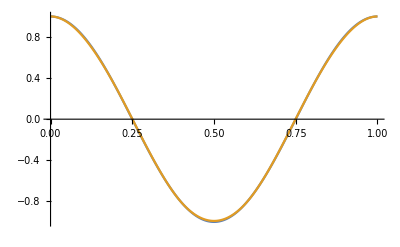

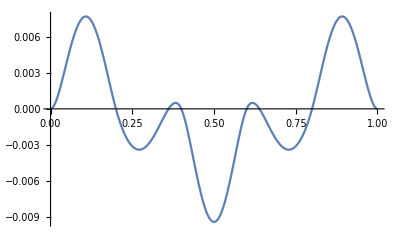

```mathematica
(*Курсов проект по Числен анализ*)
(*Изготвил: Росиана Лъджева, факултетен номер: 81461*)

n=5;

(*функцията,която ще бъде интерполирана от търсения кубичен сплайн*)
f[t_]:= Cos[2*Pi*t]; 

(*генерираме интерполационните възли*)
Do[x[k]=k/n,{k,0,n}];

(*delta e разстоянието между всеки два съседни възела*)
delta=1/n;

(*Имаме система, която се решава по метода на прогонката*) 
(*Изчисляваме коефициентите*) 
Do[d[k]=f[x[k]],{k,0,n}];
coefA=1/delta;
coefB=4/delta;
coefC=1/delta;
Do[value[k]=3*(d[k]-d[k-1])/delta^2+3*(d[k+1]-d[k])/delta^2,{k,1,n-1}];

(*намираме alpha и beta*)
alpha[1]=-coefC/coefB;
beta[1]=value[1]/coefB;

(*намираме коефициентите alpha(k) и beta(k) чрез метода на прогонката - прав ход*)
Do[alpha[k]=-coefC/(coefA*alpha[k-1]+coefB),{k,2,n-1}];
Do[beta[k]=(value[k]-coefA*beta[k-1])/(coefA*alpha[k-1]+coefB),{k,2,n-1}];

(*т.к. имаме пълна кубична интерполация: d0 = f'(x0), dn =f'(xn)*) 
c[0] = f'[x[0]];
c[n] = f'[x[n]];
c[n-1]=beta[n-1];

(*обратен ход на прогонката*)
Do[c[k]=alpha[k]*c[k+1]+beta[k],{k,n-2,1,-1}];
Do[a[k]=c[k+1]/delta^2+c[k]/delta^2+2*(d[k]-d[k+1])/delta^3,{k,0,n-1}];
Do[b[k]=(d[k+1]-d[k])/delta^2-c[k]/delta,{k,0,n-1}];


(*общ вид на полиномите, които интерполират f(t) във всеки подинтервал на [0, 1], определен от два последователни интерполационни възела*)
Do[sp[k,q_]=a[k]*(q-x[k])^2*(q-x[k+1])+b[k]*(q-x[k])^2+c[k]*(q-x[k])+f[x[k]],{k,0,n-1}];
(*p or sp !!!!!!!!!!!!!!!!!!!!!*)
(*ALSO DEFINITION BUG!!!! [k, q_] k WITHOUT UNDERSCORE*)
(*рекурсивно построяване на кубичния сплайн за f(t), чрез интерполиращите полиноми за всеки един интервал*)
(* t<=x[i+1] or t<x[i+1] *)
rec[i_,t_]:=If[i≤n-1,If[t≥x[i]&&t≤x[i+1],sp[i,t],rec[i+1,t]]];
s[t_]:=rec[0,t];

(*изчертаване на графиките на функцията и сплайн функцията*)
Plot[{f[t],s[t]}, {t, 0, 1}, PlotPoints->300]

(*изчертаване на графиката на грешката (разликата от функцията и сплайн функцията)*)
Plot[f[t]-s[t] , {t, 0, 1}, PlotRange->All]
```